```mathematica
n1=1;"$ player";
n2=1;"MG player";
n3=3;"Back ground";
n=n1+n2+n3;
m=2;
P=2^m;
T=2000-1;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=10;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
W=Table[190,{i,1,n}];
c=Table[100,{i,1,n}];
NStock=Table[9,{i,1,n},{i,1,2}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
Tinfor=Table[0,{i,1,P}];
Onetimes=Table[0,{i,1,P}];
CondionPinfor=Table[0,{i,1,P}];
BScollect=Table[0,{i,1,n}];
"initial set";
Do[
Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^P-1}],2,P]];
Do[Action⟦1,k⟧=(2*Action⟦1,k⟧-1),{k,1,P}];
RandomStrategy=Action;
AgentStrategy⟦i,s⟧=Flatten[RandomStrategy,1],{s,1,S},{i,1,n}]
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
```

```mathematica
(Label[begin];
```

```mathematica
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
```

```mathematica
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
```

```mathematica
BS
```

{{{1,-1,-1,1},{1,-1,-1,1}},{{-1,-1,1,-1},{-1,-1,1,-1}},{{-1,1,-1,-1},{1,1,1,1}},{{-1,-1,1,1},{-1,-1,1,1}},{{1,-1,-1,-1},{1,-1,-1,-1}}}

```mathematica
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
"signal=UnitStep[MarketAction]";
```

```mathematica
"match order & Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,Do[c⟦i⟧=100,{i,1,n}];Do[NStock⟦i,2⟧=9,{i,1,n}];Do[W⟦i⟧=190,{i,1,n}];,
Do[NStock⟦i,1⟧=NStock⟦i,2⟧,{i,1,n}];
ap={};
an={};
Do[If[Positive[BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧],AppendTo[ap,i],AppendTo[an,i]],{i,1,n}];
If[Length[ap]>Length[an],ap1=RandomSample[ap,Length[an]];Do[c⟦ap1⟦i⟧⟧=c⟦ap1⟦i⟧⟧-BS⟦ap1⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧),{i,1,Length[an]}];
Do[NStock⟦ap1⟦i⟧,2⟧=NStock⟦ap1⟦i⟧,1⟧+BS⟦ap1⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,Length[an]}];Do[c⟦an⟦i⟧⟧=c⟦an⟦i⟧⟧-BS⟦an⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧),{i,1,Length[an]}];
Do[NStock⟦an⟦i⟧,2⟧=NStock⟦an⟦i⟧,1⟧+BS⟦an⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,Length[an]}],
an1=RandomSample[an,Length[ap]];
Do[c⟦ap⟦i⟧⟧=c⟦ap⟦i⟧⟧-BS⟦ap⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧),{i,1,Length[ap]}];
Do[NStock⟦ap⟦i⟧,2⟧=NStock⟦ap⟦i⟧,1⟧+BS⟦ap⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,Length[ap]}];
Do[c⟦an1⟦i⟧⟧=c⟦an1⟦i⟧⟧-BS⟦an1⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧),{i,1,Length[ap]}];
Do[NStock⟦an1⟦i⟧,2⟧=NStock⟦an1⟦i⟧,1⟧+BS⟦an1⟦i⟧,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,Length[ap]}];];
Do[W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);,{i,1,n}];];
```

```mathematica
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦i,s⟧=0,{s,1,S},{i,1,n1}];,
Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}];]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Break,Goto[begin]];)//AbsoluteTiming
```

{24.03737,Null}

```mathematica
N[{c⟦1⟧-100,9*(Price⟦T⟧-10),(NStock⟦1,2⟧-9)*Price⟦T⟧,Price⟦T⟧,(NStock⟦1,2⟧-9)}]
```

{191.096,-8.95533,-45.0248,9.00496,-5.}

```mathematica
N[W⟦1⟧-190]
```

137.116

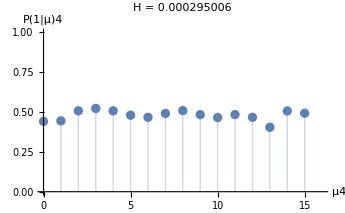

```mathematica
"P(1|μ4),P(1|μ6)";
Do[Tinfor⟦μ⟧=Tinfor⟦μ⟧+KroneckerDelta[mu⟦t⟧,μ-1];
Onetimes⟦μ⟧=Onetimes⟦μ⟧+UnitStep[A⟦t⟧]*KroneckerDelta[mu⟦t⟧,μ-1];,{t,Floor[T/2],T},{μ,1,P}];
"Tinfor";
Do[CondionPinfor⟦μ⟧=Onetimes⟦μ⟧/Tinfor⟦μ⟧,{μ,1,P}];
"prediction  H=Σ_(μ = 0)^(P - 1)ρ^μ<A|μ>^2,ρ^μ=T_μ/T";
Aonμ=0;
H=0;
Do[Do[Aonμ=Aonμ+A⟦t⟧*KroneckerDelta[mu⟦t⟧,μ-1],{t,Floor[T/2],T}];
Aonμ=Aonμ/Tinfor⟦μ⟧;
H=H+Tinfor⟦μ⟧/(T-Floor[T/2])*(Aonμ)^2;,{μ,1,P}]
f0=ListPlot[Table[{μ-1,CondionPinfor⟦μ⟧},{μ,1,P}],Filling
->Axis,PlotRange->{{0,P},{0,1}},AxesLabel-> {"μ"<>ToString[m],"P(1|μ)"<>ToString[m]},PlotLabel->"H = "<>ToString[N[H/n]]]
```

```mathematica
BScollect;
```

```mathematica
Q=1/n Sum[(2/T*BScollect⟦i⟧)^2,{i,1,n}]//N
```

0.438852

```mathematica
"Anylize   P(t+1)-P(t)=r(t)=(A (t))/λ   P(0)=10";
```

```mathematica
N[(Price⟦T⟧-10)*9]
```

28.6571

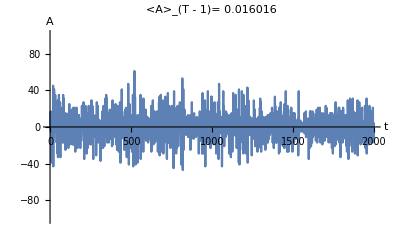

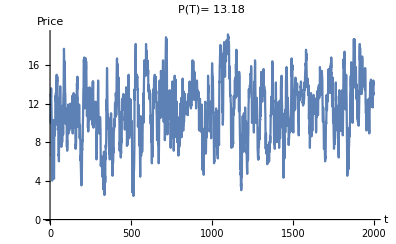

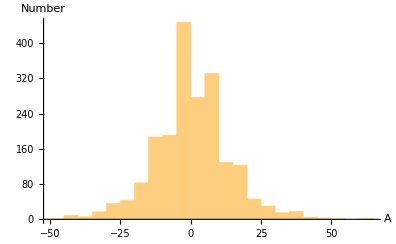

```mathematica
t1=0;
t2=T;
f1=ListPlot[A,AxesLabel->{"t","A"},PlotRange->{{t1,t2},{-n,n}},Joined->True,PlotLabel->"<A>_(T - 1)= "<>ToString[N[Mean[A⟦t1+1;;t2-1⟧]]]]
f2=ListPlot[Price⟦t1+1;;t2⟧,AxesLabel->{"t","Price"},PlotRange->Automatic,Joined->True,PlotLabel->"P(T)= "<>ToString[N[Price⟦T⟧,4]]]
f3=Histogram[A⟦t1+1;;t2⟧,AxesLabel->{"A","Number"}]
```

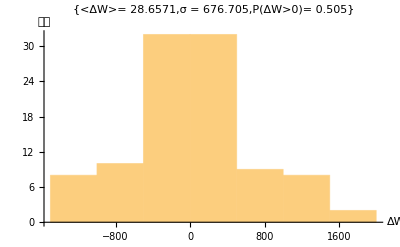

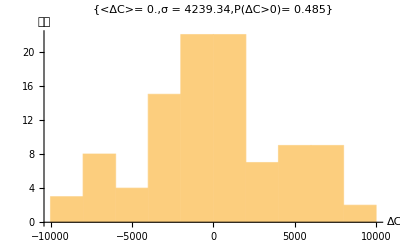

0.0155078

```mathematica
f4=Histogram[W-190,Automatic,AxesLabel->{ΔW,人數},PlotLabel->{ "<ΔW>= "<>ToString[N[Mean[W-190]]],"σ = "<>ToString[N[StandardDeviation[W-190]]],"P(ΔW>0)= "<>ToString[N[1/n Total[UnitStep[W-190]],3]]}]
f5=Histogram[c-100,Automatic,AxesLabel->{ΔC,人數},PlotLabel->{ "<ΔC>= "<>ToString[N[Mean[c-100]]],"σ = "<>ToString[N[StandardDeviation[c-100]]],"P(ΔC>0)= "<>ToString[N[1/n Total[UnitStep[c-100]],3]]}]

mu⟦t1+1;;t2⟧;
Mean[A⟦t1+1;;t2⟧]//N
```

```mathematica
N[{W⟦1⟧,W⟦2⟧},2]
```

{250.,-560.}